## Exercises: Speed and Memory Performance

### Exercise1 After entering the following definitions for f, use Timing and ListLogPlot to make a plot with a logarithmic vertical scale of the time needed to evaluate f[n] for n from 1 to 30:

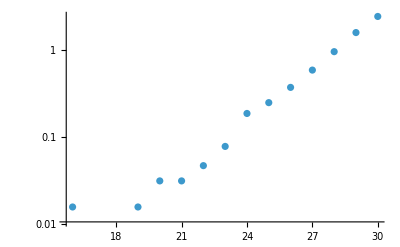

```mathematica
f[0]=1;
f[1]=1;
f[n_]:=f[n-1]+f[n-2]

ListLogPlot[Table[{n,First[Timing[f[n]]]},{n,30}]]
```

```mathematica
ClearAll[f]
```

### Exercise2 Modify this program to use Sow and Reap to accumulate the final result rather than Append:

```mathematica
n=0;
counter=0;
Reap[
While[counter<10,n=n+1;
If[PrimeQ[n],Sow[n];counter++]]][[2,1]]
```

{2,3,5,7,11,13,17,19,23,29}

## Exercises: Monitoring and Debugging

### Exercise1 Use Reap and Sow to modify this program so that the result of the evaluation includes the list of x’s that come up during the calculation:

```mathematica
Nest[Function[x,x+1],0,10]
```

10

```mathematica
Reap[Nest[Function[x,Sow[x]+1],0,10]]
```

{10,{{0,1,2,3,4,5,6,7,8,9}}}

### Exercise2 Modify this program using Monitor and ProgressIndicator so that a progress indicator bar showing the current value of k is displayed while the program is running:

```mathematica
result=0;For[k=0,k<=10,k++,result=result+k;Pause[0.2]];result
```

```mathematica
Monitor[result=0;For[k=0,k<=10,k++,result=result+k;Pause[0.2]];result ,ProgressIndicator[k,{0,10}]]
```

55

```mathematica
Compile[{{x,_Real,1}},Length[x]]
```

CompiledFunction[…]

```mathematica
Timing[3+4]
```

{0.,7}

```mathematica
Monitor[Table[Pause[1];k,{k,5}],k]
```

{1,2,3,4,5}

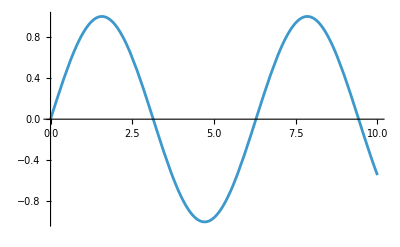
{-Graphics-,{{2.04082×10^-7,0.196287,0.409084,0.607779,0.802576,1.01388,1.21109,1.42481,1.63463,1.83035,2.04257,2.2407,2.43493,2.64567,2.84231,3.05546,3.26471,3.45986,3.67151,3.86907,4.08314,4.29331,4.48938,4.70196,4.90044,5.09502,5.30611,5.5031,5.7166,5.9262,6.1217,6.33371,6.53162,6.72563,6.93616,7.13258,7.34551,7.54434,7.73927,7.95071,8.14805,8.3619,8.57186,8.76771,8.98007,9.17833,9.3727,9.58357,9.78034,10.,0.0981434,0.705178,0.908231,1.11249,1.31795,1.52972,1.73249,1.93646,2.14164,2.33781,3.77029,3.97611,4.18823,4.39135,4.59567,4.8012,4.99773,5.20057,5.40461,5.60985,7.03437,7.23904,7.44492,7.6418,7.84499,8.04938,8.25498,8.46688,8.66978,9.89017,0.0490718,0.656478,0.855404,1.06319,1.26452,1.47726,1.68356,1.8834,2.09211,2.28926,3.7209,3.92259,4.13568,4.34233,4.54253,4.75158,4.94908,5.14779,5.35536,5.55647,6.98526,7.18581,7.39522,7.59307,7.79213,8.00005,8.20152,8.41439,8.62082,9.83526,0.961058,1.16179,1.37138,1.58217,1.78142,1.98952,4.02962,4.24077,4.44036,4.64882,4.85082,5.04637,5.25334,7.08347,7.29228,7.49463,7.69054,7.89785,8.09872,8.30844,9.94509,0.024536,0.632129,0.82899,1.03854,1.23781,1.45104,1.65909,1.85687,2.06734,2.26498,3.69621,3.89583,4.10941,4.31782,4.51595,4.72677,4.92476,5.12141,5.33073,5.52979,6.96071,7.15919,7.37036,7.5687,7.7657,7.97538,8.17478,8.38815,8.59634,9.8078,0.934644,1.13714,1.34466,1.55595,1.75695,1.96299,4.00287,4.2145,4.41586,4.62224,4.82601,5.02205,5.22695,7.05892,7.26566,7.46978,7.66617,7.87142,8.07405,8.28171,9.91763,1.29124,1.50349,1.70802,1.90993,4.36684,4.5691,4.77639,4.97341,7.42007,7.61744,7.81856,8.02472,8.22825,1.39809,1.6084,1.80588,4.46487,4.67539,4.87563,7.7149,7.92428,8.12339,9.97254,0.0122681,0.619954,0.815783,1.02621,1.22445,1.43792,1.64686,1.84361,2.05496,2.25284,3.68386,3.88245,4.09628,4.30557,4.50267,4.71437,4.9126,5.10821,5.31842,5.51644,6.94843,7.14589,7.35794,7.55652,7.75249,7.96305,8.16142,8.37503,8.5841,9.79407,0.921437,1.12481,1.33131,1.54283,1.74472,1.94972,3.98949,4.20136,4.4036,4.60896,4.8136,5.00989,5.21376,7.04664,7.25235,7.45735,7.65399,7.85821,8.06172,8.26834,9.9039,1.27788,1.49038,1.69579,1.89667,4.35458,4.55581,4.76399,4.96125,7.40764,7.60525,7.80535,8.01238,8.21488,1.38474,1.59529,1.79365,4.45262,4.6621,4.86322,7.70272,7.91107,8.11105,9.95881,1.46415,1.67132,4.52924,4.73918,7.77892,7.98771,1.35802,1.56906,4.63553,4.83841,7.67835,7.88464,1.5166,1.72025,4.58238,4.7888,7.83178,1.41145,1.62151,4.68867,7.72709,7.9375,9.98627,0.00613415,0.613866,0.80918,1.02005,1.21777,1.43137,1.64074,1.83698,2.04877,2.24677,3.67769,3.87576,4.08971,4.29944,4.49602,4.70816,4.90652,5.10162,5.31227,5.50977,6.9423,7.13923,7.35172,7.55043,7.74588,7.95688,8.15474,8.36847,8.57798,9.78721,0.914834,1.11865,1.32463,1.53627,1.7386,1.94309,3.9828,4.19479,4.39747,4.60231,4.8074,5.00381,5.20716,7.04051,7.2457,7.45114,7.6479,7.8516,8.05555,8.26166,9.89704,1.2712,1.48382,1.68967,1.89003,4.34846,4.54917,4.75778,4.95516,7.40143,7.59916,7.79874,8.00621,8.2082,1.37806,1.58873,1.78753,4.44649,4.65546,4.85702,7.69663,7.90446,8.10489,9.95195,1.45759,1.66521,4.5226,4.73297,7.77231,7.98155,1.35134,1.5625,4.62889,4.83221,7.67226,7.87803,1.51005,1.71414,4.57574,4.78259,7.82517,1.40477,1.61496,4.68203,7.721,7.93089,9.97941,1.65298,4.72057,7.75909,1.54939,4.6156,7.86481,1.49693,4.77019,7.81195,1.60184,4.66875,7.91767,4.74538,7.78552,1.57562,4.64217,7.89124,1.52316,7.83838,1.62807,4.69532,9.99314,0.00306718,0.610823,0.805878,1.01697,1.21443,1.42809,1.63769,1.83366,2.04567,2.24374,3.6746,3.87242,4.08643,4.29638,4.4927,4.70506,4.90348,5.09832,5.30919,5.50644,6.93923,7.1359,7.34862,7.54738,7.74257,7.9538,8.1514,8.36519,8.57492,9.78378,0.911532,1.11557,1.32129,1.533,1.73554,1.93978,3.97945,4.19151,4.39441,4.59899,4.8043,5.00077,5.20386,7.03744,7.24237,7.44803,7.64485,7.8483,8.05247,8.25832,9.8936,1.26786,1.48054,1.68662,1.88672,4.34539,4.54585,4.75468,4.95212,7.39832,7.59612,7.79543,8.00313,8.20486,1.37472,1.58545,1.78447,4.44343,4.65214,4.85392,7.69358,7.90116,8.1018,9.94852,1.45431,1.66215,4.51928,4.72987,7.769,7.97846,1.348,1.55922,4.62557,4.82911,7.66922,7.87473,1.50677,1.71108,4.57242,4.77949,7.82187,1.40143,1.61168,4.67871,7.71795,7.92759,9.97597,1.64992,4.71747,7.75579,1.54611,4.61228,7.86151,1.49366,4.76709,7.80865,1.59856,4.66542,7.91437,4.74228,7.78222,1.57234,4.63885,7.88794,1.51988,7.83508,1.62479,4.692,9.9897,4.71126,1.53955,7.8549,7.80204,1.59201,4.65878,4.73607,1.56578,7.88133,1.51333,7.82847,1.61824,4.68535,4.72367,1.55267,7.86812,7.81526,1.60512,4.67207,4.74848,1.57889,7.89455,7.84169,4.69864,9.99657}}}

```mathematica
Reap[Plot[Sin[x],{x,0,10},EvaluationMonitor:>Sow[x]]]
```

```mathematica
Table[2Echo[x],{x,3}]
```

1

2

3

{2,4,6}

```mathematica
Monitor[Table[Pause[1];x+1,{x,6}],x]
```

{2,3,4,5,6,7}

## Exercises: Datasets

### Exercise1 Add a new entry for cherry wood with a density of 630 and hardness of 4430 to the dataset below:

```mathematica
woodData=Dataset[<|"birch"-><|"density"->670,"hardness"->5600|>,"cedar"-><|"density"->380,"hardness"->4000|>,"maple"-><|"density"->700,"hardness"->3100|>|>]
```

```mathematica
woodData=Dataset[<|"birch"-><|"density"->670,"hardness"->5600|>,"cedar"-><|"density"->380,"hardness"->4000|>,"maple"-><|"density"->700,"hardness"->3100|>,"Cherry wood" -><|"density" -> 630, "hardness" -> 4430 |>|>]
```

### Exercise2 Round the entries to the nearest hundred and add “approximate” before the column names:

```mathematica
woodData=Dataset[Round[<|"birch"-><|"Approx. density"->670,"Approx. hardness"->5600|>,"cedar"-><|"Approx. density"->380,"Approx. hardness"->4000|>,"maple"-><|"Approx. density"->700,"Approx. hardness"->3100|>,"cherry"-><|"Approx. density"->630,"Approx. hardness"->4430|>|>,100]]
```

### Exercise3 Select entries whose density is divisible by 7:

```mathematica
woodData=Dataset[<|"birch"-><|"density"->670,"hardness"->5600|>,"cedar"-><|"density"->380,"hardness"->4000|>,"maple"-><|"density"->700,"hardness"->3100|>,"cherry"-><|"density"->630,"hardness"->4430|>|>]
```

```mathematica
Select[woodData,Mod[#density, 7] == 0 &]
```

## Exercises: Controlling Evaluation

### Exercise1 Add a value of the PlotLabel option to this input so that Solve[4x==x^3,x] appears as a label on the plot:

```mathematica
Plot[{Callout[4x,"solution",Automatic,2],x^3},{x,0,3}]
```

-Graphics-

```mathematica
Plot[{Callout[4x,"solution",Automatic,2],x^3},{x,0,3}, PlotLabel->HoldForm[Solve[4x==x^3,x]]]
```

-Graphics-

### Exercise2 Use Function to change this input so that the result shows the evaluated values of x and y:

```mathematica
Block[{x=2,y=2},Defer[x+y]]
```

x+y

```mathematica
Block[{x=2,y=2},Function[{p,q},Defer[p+p]][x,y]]
```

2+2

### Exercise3 Use Function to change this input so that the result is a list containing the even integers in the unevaluated list:

```mathematica
Select[Unevaluated[{1,2,3,4,Abort[]}],EvenQ]
```

$Aborted

```mathematica
Select[Unevaluated[{1,2,3,4,Abort[]}],Function[x,EvenQ[Unevaluated[x]],HoldAll]]
```

{2,4}

### Exercise4 Define a rule for f[p_List,n_Integer] that returns Table[pn,{x,5}], where pn is the element at position n in the list p, and that will work even if x has a global value, and without evaluating any other elements in p. For example:

```mathematica
x=99;f[{x,x^2,Abort[]},2]
```

```mathematica
SetAttributes[f,HoldAll]
f[p_List,n_Integer]:=Extract[Unevaluated[p],n,Function[pn,Table[pn,{x,5}],HoldAll]]
x=99;f[{x,x^2,Abort[]},2]
ClearAll[f,x]
```

{1,4,9,16,25}

## Exercises: Nonstandard Evaluation

### Exercise1 Define a function f that takes one argument and that returns the head of that argument; for example:

```mathematica
SetAttributes[f,HoldAll]
f[p_]:=Head[Unevaluated[p]]
f[2+2]
f[Abort[]]
f[Timing[]]
```

Plus

Abort

Timing

### Exercise2 Define a rule for f[x_Symbol,p_] that assigns ToString[p] where p is evaluated, and that works even if x already has a global value; for example:

```mathematica
x=99;f[x,Table[k,{k,3}]];x
```

```mathematica
SetAttributes[f,HoldFirst]
f[x_Symbol,p_]:=(x=ToString[p])
x=99;f[x,Table[k,{k,3}]];x
ClearAll[f,x]
```

{1, 2, 3}